```mathematica
colfunc=ColorData["AvocadoColors"];
poc[c_,z_]:=Expand@Sum[bin[z,k],{k,0,c}]
pocroots[n_]:=If[(c=Exponent[f=poc[n,z],z])==0,{},If[c==1,List@NRoots[f==0,z][[2]],List@@NRoots[f==0,z][[All,2]]]]
pocrootsa[n_]:=pocrootsa[n]=If[(c=Exponent[f=poc[n,z],z])==0,{},If[c==1,List@Roots[f==0,z][[2]],List@@Roots[f==0,z][[All,2]]]]
Clear[px,pz,t]
t[n_, a_, b_] := t[n,a,b]=b(Floor[n/b]-Floor[(n-1)/b])-a(Floor[n/a]-Floor[(n-1)/a])
px[n_,a_, b_, k_]:=px[n,a,b,k]=Sum[t[j,a,b]/j px[n-j,a,b,k-1],{j,1,n-1}]
px[n_,a_, b_, 1]:=t[n,a,b]/n
px[n_,a_, b_, 0]:=0
pz[n_, a_, b_, z_] := Sum[ z^k/k! px[n,a,b,k],{k,0,n}]
pz[n_, a_, b_,0] := 1
pz[0, a_, b_,z_] := 1
pocx[m_,a_,b_,z_]:=Sum[pz[n,a,b,z],{n,0,m}]
pocxrootsa[n_,a_,b_]:=pocxrootsa[n,a,b]=If[(c=Exponent[f=pocx[n,a,b,z],z])==0,{},If[c==1,List@Roots[f==0,z][[2]],List@@Roots[f==0,z][[All,2]]]]
pocc[c_,z_]:=Expand@Sum[Pochhammer[z,k]/k!,{k,0,c}]
poccrootsa[n_]:=poccrootsa[n]=If[(c=Exponent[f=pocc[n,z],z])==0,{},If[c==1,List@Roots[f==0,z][[2]],List@@Roots[f==0,z][[All,2]]]]
```

```mathematica
poc[20,z]/.z->-3
```

121

```mathematica
N@Sum[-1/r,{r,pocrootsa[200]}]
```

0.690653-6.93889×10^-18 ⅈ

```mathematica
Log[2.]
```

0.693147

```mathematica
N@Sum[-1/r,{r,pocrootsa[400]}]
```

0.691899+0. ⅈ

```mathematica
N[pocrootsa[400]]
```

{-0.9793-0.434766 ⅈ,-0.9793+0.434766 ⅈ,-0.835982-1.34513 ⅈ,-0.835982+1.34513 ⅈ,-0.606245-2.32191 ⅈ,-0.606245+2.32191 ⅈ,-0.319084-3.35336 ⅈ,-0.319084+3.35336 ⅈ,0.0139939-4.42949 ⅈ,0.0139939+4.42949 ⅈ,0.386915-5.5436 ⅈ,0.386915+5.5436 ⅈ,0.795861-6.69094 ⅈ,0.795861+6.69094 ⅈ,1.23818-7.86792 ⅈ,1.23818+7.86792 ⅈ,1.71192-9.0717 ⅈ,1.71192+9.0717 ⅈ,2.21557-10.3 ⅈ,2.21557+10.3 ⅈ,2.74793-11.551 ⅈ,2.74793+11.551 ⅈ,3.30801-12.8229 ⅈ,3.30801+12.8229 ⅈ,3.89499-14.1144 ⅈ,3.89499+14.1144 ⅈ,4.50817-15.4244 ⅈ,4.50817+15.4244 ⅈ,5.14697-16.7516 ⅈ,5.14697+16.7516 ⅈ,5.81088-18.0952 ⅈ,5.81088+18.0952 ⅈ,6.49943-19.4543 ⅈ,6.49943+19.4543 ⅈ,7.21223-20.828 ⅈ,7.21223+20.828 ⅈ,7.94895-22.2157 ⅈ,7.94895+22.2157 ⅈ,8.70926-23.6167 ⅈ,8.70926+23.6167 ⅈ,9.49289-25.0304 ⅈ,9.49289+25.0304 ⅈ,10.2996-26.4562 ⅈ,10.2996+26.4562 ⅈ,11.1291-27.8935 ⅈ,11.1291+27.8935 ⅈ,11.9813-29.3419 ⅈ,11.9813+29.3419 ⅈ,12.856-30.8009 ⅈ,12.856+30.8009 ⅈ,13.7529-32.2701 ⅈ,13.7529+32.2701 ⅈ,14.6721-33.7489 ⅈ,14.6721+33.7489 ⅈ,15.6132-35.2371 ⅈ,15.6132+35.2371 ⅈ,16.5762-36.7343 ⅈ,16.5762+36.7343 ⅈ,17.561-38.24 ⅈ,17.561+38.24 ⅈ,18.5676-39.754 ⅈ,18.5676+39.754 ⅈ,19.5957-41.2758 ⅈ,19.5957+41.2758 ⅈ,20.6453-42.8053 ⅈ,20.6453+42.8053 ⅈ,21.7164-44.342 ⅈ,21.7164+44.342 ⅈ,22.8089-45.8857 ⅈ,22.8089+45.8857 ⅈ,23.9228-47.436 ⅈ,23.9228+47.436 ⅈ,25.0579-48.9928 ⅈ,25.0579+48.9928 ⅈ,26.2143-50.5557 ⅈ,26.2143+50.5557 ⅈ,27.3919-52.1245 ⅈ,27.3919+52.1245 ⅈ,28.5907-53.6989 ⅈ,28.5907+53.6989 ⅈ,29.8106-55.2786 ⅈ,29.8106+55.2786 ⅈ,31.0517-56.8635 ⅈ,31.0517+56.8635 ⅈ,32.3139-58.4532 ⅈ,32.3139+58.4532 ⅈ,33.5973-60.0476 ⅈ,33.5973+60.0476 ⅈ,34.9018-61.6465 ⅈ,34.9018+61.6465 ⅈ,36.2274-63.2495 ⅈ,36.2274+63.2495 ⅈ,37.5741-64.8565 ⅈ,37.5741+64.8565 ⅈ,38.9419-66.4673 ⅈ,38.9419+66.4673 ⅈ,40.3309-68.0816 ⅈ,40.3309+68.0816 ⅈ,41.7411-69.6993 ⅈ,41.7411+69.6993 ⅈ,43.1725-71.3201 ⅈ,43.1725+71.3201 ⅈ,44.6251-72.9438 ⅈ,44.6251+72.9438 ⅈ,46.0989-74.5703 ⅈ,46.0989+74.5703 ⅈ,47.594-76.1993 ⅈ,47.594+76.1993 ⅈ,49.1104-77.8307 ⅈ,49.1104+77.8307 ⅈ,50.6482-79.4642 ⅈ,50.6482+79.4642 ⅈ,52.2074-81.0996 ⅈ,52.2074+81.0996 ⅈ,53.788-82.7369 ⅈ,53.788+82.7369 ⅈ,55.3901-84.3757 ⅈ,55.3901+84.3757 ⅈ,57.0138-86.0159 ⅈ,57.0138+86.0159 ⅈ,58.6591-87.6572 ⅈ,58.6591+87.6572 ⅈ,60.326-89.2996 ⅈ,60.326+89.2996 ⅈ,62.0147-90.9428 ⅈ,62.0147+90.9428 ⅈ,63.7252-92.5867 ⅈ,63.7252+92.5867 ⅈ,65.4576-94.231 ⅈ,65.4576+94.231 ⅈ,67.2119-95.8755 ⅈ,67.2119+95.8755 ⅈ,68.9882-97.5202 ⅈ,68.9882+97.5202 ⅈ,70.7866-99.1647 ⅈ,70.7866+99.1647 ⅈ,72.6072-100.809 ⅈ,72.6072+100.809 ⅈ,74.4501-102.453 ⅈ,74.4501+102.453 ⅈ,76.3153-104.096 ⅈ,76.3153+104.096 ⅈ,78.203-105.738 ⅈ,78.203+105.738 ⅈ,80.1133-107.379 ⅈ,80.1133+107.379 ⅈ,82.0462-109.019 ⅈ,82.0462+109.019 ⅈ,84.0019-110.658 ⅈ,84.0019+110.658 ⅈ,85.9805-112.295 ⅈ,85.9805+112.295 ⅈ,87.9821-113.93 ⅈ,87.9821+113.93 ⅈ,90.0067-115.563 ⅈ,90.0067+115.563 ⅈ,92.0546-117.194 ⅈ,92.0546+117.194 ⅈ,94.1259-118.823 ⅈ,94.1259+118.823 ⅈ,96.2206-120.449 ⅈ,96.2206+120.449 ⅈ,98.3389-122.072 ⅈ,98.3389+122.072 ⅈ,100.481-123.693 ⅈ,100.481+123.693 ⅈ,102.647-125.31 ⅈ,102.647+125.31 ⅈ,104.837-126.924 ⅈ,104.837+126.924 ⅈ,107.051-128.534 ⅈ,107.051+128.534 ⅈ,109.29-130.14 ⅈ,109.29+130.14 ⅈ,111.553-131.742 ⅈ,111.553+131.742 ⅈ,113.84-133.341 ⅈ,113.84+133.341 ⅈ,116.153-134.934 ⅈ,116.153+134.934 ⅈ,118.49-136.523 ⅈ,118.49+136.523 ⅈ,120.853-138.107 ⅈ,120.853+138.107 ⅈ,123.241-139.686 ⅈ,123.241+139.686 ⅈ,125.655-141.26 ⅈ,125.655+141.26 ⅈ,128.094-142.828 ⅈ,128.094+142.828 ⅈ,130.559-144.39 ⅈ,130.559+144.39 ⅈ,133.05-145.946 ⅈ,133.05+145.946 ⅈ,135.568-147.496 ⅈ,135.568+147.496 ⅈ,138.113-149.039 ⅈ,138.113+149.039 ⅈ,140.684-150.575 ⅈ,140.684+150.575 ⅈ,143.282-152.105 ⅈ,143.282+152.105 ⅈ,145.907-153.627 ⅈ,145.907+153.627 ⅈ,148.56-155.141 ⅈ,148.56+155.141 ⅈ,151.241-156.647 ⅈ,151.241+156.647 ⅈ,153.949-158.145 ⅈ,153.949+158.145 ⅈ,156.686-159.635 ⅈ,156.686+159.635 ⅈ,159.452-161.116 ⅈ,159.452+161.116 ⅈ,162.246-162.587 ⅈ,162.246+162.587 ⅈ,165.07-164.05 ⅈ,165.07+164.05 ⅈ,167.923-165.502 ⅈ,167.923+165.502 ⅈ,170.806-166.945 ⅈ,170.806+166.945 ⅈ,173.718-168.377 ⅈ,173.718+168.377 ⅈ,176.661-169.798 ⅈ,176.661+169.798 ⅈ,179.635-171.208 ⅈ,179.635+171.208 ⅈ,182.64-172.607 ⅈ,182.64+172.607 ⅈ,185.677-173.994 ⅈ,185.677+173.994 ⅈ,188.745-175.368 ⅈ,188.745+175.368 ⅈ,191.845-176.73 ⅈ,191.845+176.73 ⅈ,194.978-178.08 ⅈ,194.978+178.08 ⅈ,198.144-179.415 ⅈ,198.144+179.415 ⅈ,201.343-180.737 ⅈ,201.343+180.737 ⅈ,204.577-182.044 ⅈ,204.577+182.044 ⅈ,207.844-183.337 ⅈ,207.844+183.337 ⅈ,211.146-184.614 ⅈ,211.146+184.614 ⅈ,214.484-185.876 ⅈ,214.484+185.876 ⅈ,217.857-187.122 ⅈ,217.857+187.122 ⅈ,221.267-188.351 ⅈ,221.267+188.351 ⅈ,224.713-189.562 ⅈ,224.713+189.562 ⅈ,228.197-190.756 ⅈ,228.197+190.756 ⅈ,231.719-191.931 ⅈ,231.719+191.931 ⅈ,235.279-193.087 ⅈ,235.279+193.087 ⅈ,238.879-194.224 ⅈ,238.879+194.224 ⅈ,242.518-195.341 ⅈ,242.518+195.341 ⅈ,246.198-196.436 ⅈ,246.198+196.436 ⅈ,249.919-197.51 ⅈ,249.919+197.51 ⅈ,253.681-198.562 ⅈ,253.681+198.562 ⅈ,257.487-199.591 ⅈ,257.487+199.591 ⅈ,261.336-200.596 ⅈ,261.336+200.596 ⅈ,265.229-201.577 ⅈ,265.229+201.577 ⅈ,269.167-202.532 ⅈ,269.167+202.532 ⅈ,273.152-203.461 ⅈ,273.152+203.461 ⅈ,277.183-204.362 ⅈ,277.183+204.362 ⅈ,281.262-205.236 ⅈ,281.262+205.236 ⅈ,285.39-206.08 ⅈ,285.39+206.08 ⅈ,289.567-206.895 ⅈ,289.567+206.895 ⅈ,293.796-207.678 ⅈ,293.796+207.678 ⅈ,298.077-208.429 ⅈ,298.077+208.429 ⅈ,302.412-209.147 ⅈ,302.412+209.147 ⅈ,306.801-209.83 ⅈ,306.801+209.83 ⅈ,311.246-210.477 ⅈ,311.246+210.477 ⅈ,315.749-211.086 ⅈ,315.749+211.086 ⅈ,320.311-211.657 ⅈ,320.311+211.657 ⅈ,324.933-212.188 ⅈ,324.933+212.188 ⅈ,329.617-212.677 ⅈ,329.617+212.677 ⅈ,334.365-213.122 ⅈ,334.365+213.122 ⅈ,339.179-213.523 ⅈ,339.179+213.523 ⅈ,344.06-213.876 ⅈ,344.06+213.876 ⅈ,349.011-214.18 ⅈ,349.011+214.18 ⅈ,354.034-214.433 ⅈ,354.034+214.433 ⅈ,359.131-214.633 ⅈ,359.131+214.633 ⅈ,364.304-214.778 ⅈ,364.304+214.778 ⅈ,369.557-214.864 ⅈ,369.557+214.864 ⅈ,374.892-214.889 ⅈ,374.892+214.889 ⅈ,380.312-214.851 ⅈ,380.312+214.851 ⅈ,385.82-214.747 ⅈ,385.82+214.747 ⅈ,391.42-214.573 ⅈ,391.42+214.573 ⅈ,397.115-214.325 ⅈ,397.115+214.325 ⅈ,402.909-214.001 ⅈ,402.909+214.001 ⅈ,408.807-213.596 ⅈ,408.807+213.596 ⅈ,414.812-213.106 ⅈ,414.812+213.106 ⅈ,420.931-212.525 ⅈ,420.931+212.525 ⅈ,427.169-211.85 ⅈ,427.169+211.85 ⅈ,433.531-211.075 ⅈ,433.531+211.075 ⅈ,440.024-210.193 ⅈ,440.024+210.193 ⅈ,446.655-209.198 ⅈ,446.655+209.198 ⅈ,453.432-208.084 ⅈ,453.432+208.084 ⅈ,460.363-206.841 ⅈ,460.363+206.841 ⅈ,467.458-205.462 ⅈ,467.458+205.462 ⅈ,474.728-203.937 ⅈ,474.728+203.937 ⅈ,482.184-202.255 ⅈ,482.184+202.255 ⅈ,489.84-200.404 ⅈ,489.84+200.404 ⅈ,497.71-198.37 ⅈ,497.71+198.37 ⅈ,505.813-196.138 ⅈ,505.813+196.138 ⅈ,514.166-193.692 ⅈ,514.166+193.692 ⅈ,522.794-191.009 ⅈ,522.794+191.009 ⅈ,531.722-188.068 ⅈ,531.722+188.068 ⅈ,540.98-184.842 ⅈ,540.98+184.842 ⅈ,550.606-181.298 ⅈ,550.606+181.298 ⅈ,560.643-177.397 ⅈ,560.643+177.397 ⅈ,571.145-173.095 ⅈ,571.145+173.095 ⅈ,582.179-168.334 ⅈ,582.179+168.334 ⅈ,593.827-163.042 ⅈ,593.827+163.042 ⅈ,606.2-157.129 ⅈ,606.2+157.129 ⅈ,619.443-150.472 ⅈ,619.443+150.472 ⅈ,633.758-142.908 ⅈ,633.758+142.908 ⅈ,649.442-134.199 ⅈ,649.442+134.199 ⅈ,666.956-123.985 ⅈ,666.956+123.985 ⅈ,687.102-111.665 ⅈ,687.102+111.665 ⅈ,711.506-96.086 ⅈ,711.506+96.086 ⅈ,744.694-74.3335 ⅈ,744.694+74.3335 ⅈ}

```mathematica
N@Product[1-1/r,{r,pocrootsa[400]}]
```

2.+7.49717×10^-17 ⅈ

```mathematica
N@2^ZetaZero[1]
```

-1.31714-0.514916 ⅈ

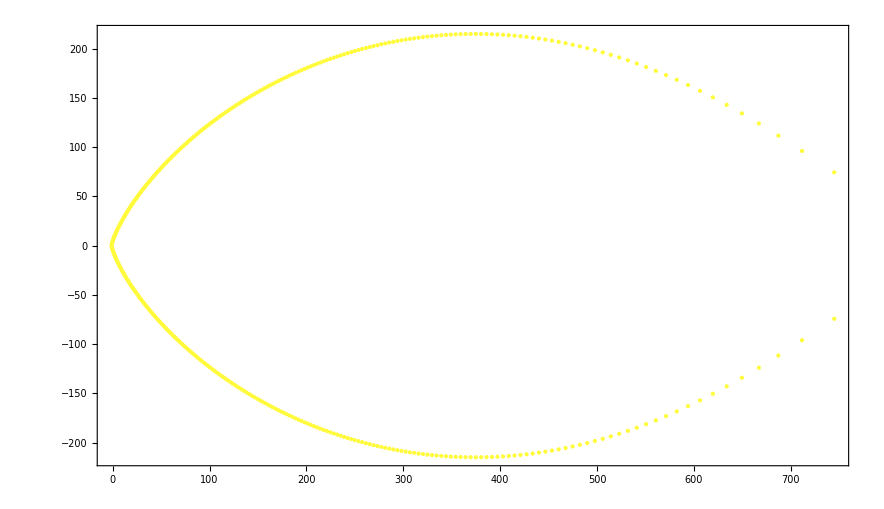

```mathematica
colfunc=ColorData["AvocadoColors"];
pts1=Table[{colfunc[100],Point[{Re[#],Im[#]}]}&/@N@pocrootsa[400],{n,1,1}];
Graphics[pts1,Frame->True]
```

```mathematica
Sum[Binomial[-ZetaZero[1],k],{k,0,Infinity}]
```

Sum::div: Sum does not converge.

∑_(k=0)^∞ Binomial[-ZetaZero[1],k]

Sum::div: Sum does not converge.

∑_(k=0)^∞ Binomial[-0.5+14. ⅈ,k]

```mathematica
1/2^ZetaZero[1]
```

2^(-ZetaZero[1])

```mathematica
Clear[px,pz,t]
t[n_, a_, b_] := t[n,a,b]=b(Floor[n/b]-Floor[(n-1)/b])-a(Floor[n/a]-Floor[(n-1)/a])
px[n_,a_, b_, k_]:=px[n,a,b,k]=Sum[t[j,a,b]/j px[n-j,a,b,k-1],{j,1,n-1}]
px[n_,a_, b_, 1]:=t[n,a,b]/n
px[n_,a_, b_, 0]:=0
pz[n_, a_, b_, z_] := Sum[ z^k/k! px[n,a,b,k],{k,0,n}]
pz[n_, a_, b_,0] := 1
pz[0, a_, b_,z_] := 1
```

```mathematica
N@pocxrootsa[200,3,1]
```

{-1204.08,-1135.59,-1080.62,-1032.89,-989.963,-950.57,-913.949,-879.593,-847.143,-816.333,-786.96,-758.862,-731.91,-705.997,-681.034,-656.945,-633.666,-611.141,-589.321,-568.163,-547.631,-527.689,-508.307,-489.459,-471.12,-453.267,-435.881,-418.941,-402.433,-386.338,-370.644,-355.337,-340.404,-325.833,-311.614,-297.737,-284.192,-270.971,-258.065,-245.466,-233.167,-221.162,-209.443,-198.004,-186.84,-175.946,-165.315,-154.943,-144.826,-134.958,-125.336,-115.956,-106.813,-97.9042,-89.2261,-80.7753,-72.5486,-64.5429,-56.7553,-49.1832,-41.8239,-34.6748,-27.7336,-20.998,-14.4656,-8.13457,-0.780608-1.08241 ⅈ,-0.780608+1.08241 ⅈ,-0.37672-2.13676 ⅈ,-0.37672+2.13676 ⅈ,0.116421-3.22249 ⅈ,0.116421+3.22249 ⅈ,0.685648-4.33882 ⅈ,0.685648+4.33882 ⅈ,1.32446-5.48178 ⅈ,1.32446+5.48178 ⅈ,2.02732-6.64776 ⅈ,2.02732+6.64776 ⅈ,2.78964-7.83337 ⅈ,2.78964+7.83337 ⅈ,3.6079-9.03544 ⅈ,3.6079+9.03544 ⅈ,4.47946-10.2512 ⅈ,4.47946+10.2512 ⅈ,5.40234-11.4784 ⅈ,5.40234+11.4784 ⅈ,6.37498-12.7148 ⅈ,6.37498+12.7148 ⅈ,7.39615-13.9588 ⅈ,7.39615+13.9588 ⅈ,8.46486-15.2087 ⅈ,8.46486+15.2087 ⅈ,9.58035-16.4631 ⅈ,9.58035+16.4631 ⅈ,10.742-17.7206 ⅈ,10.742+17.7206 ⅈ,11.9493-18.9799 ⅈ,11.9493+18.9799 ⅈ,13.2021-20.2398 ⅈ,13.2021+20.2398 ⅈ,14.4999-21.4993 ⅈ,14.4999+21.4993 ⅈ,15.8428-22.7572 ⅈ,15.8428+22.7572 ⅈ,17.2308-24.0123 ⅈ,17.2308+24.0123 ⅈ,18.6638-25.2636 ⅈ,18.6638+25.2636 ⅈ,20.142-26.5102 ⅈ,20.142+26.5102 ⅈ,21.6658-27.7508 ⅈ,21.6658+27.7508 ⅈ,23.2353-28.9844 ⅈ,23.2353+28.9844 ⅈ,24.851-30.2099 ⅈ,24.851+30.2099 ⅈ,26.5135-31.4263 ⅈ,26.5135+31.4263 ⅈ,28.2232-32.6323 ⅈ,28.2232+32.6323 ⅈ,29.9808-33.8269 ⅈ,29.9808+33.8269 ⅈ,31.787-35.0087 ⅈ,31.787+35.0087 ⅈ,33.6428-36.1765 ⅈ,33.6428+36.1765 ⅈ,35.5489-37.329 ⅈ,35.5489+37.329 ⅈ,37.5065-38.4647 ⅈ,37.5065+38.4647 ⅈ,39.5168-39.5822 ⅈ,39.5168+39.5822 ⅈ,41.5809-40.6798 ⅈ,41.5809+40.6798 ⅈ,43.7004-41.756 ⅈ,43.7004+41.756 ⅈ,45.8767-42.8089 ⅈ,45.8767+42.8089 ⅈ,48.1116-43.8366 ⅈ,48.1116+43.8366 ⅈ,50.4071-44.837 ⅈ,50.4071+44.837 ⅈ,52.7651-45.8078 ⅈ,52.7651+45.8078 ⅈ,55.1881-46.7466 ⅈ,55.1881+46.7466 ⅈ,57.6786-47.6507 ⅈ,57.6786+47.6507 ⅈ,60.2396-48.5173 ⅈ,60.2396+48.5173 ⅈ,62.8741-49.343 ⅈ,62.8741+49.343 ⅈ,65.5858-50.1244 ⅈ,65.5858+50.1244 ⅈ,68.3787-50.8575 ⅈ,68.3787+50.8575 ⅈ,71.2574-51.5379 ⅈ,71.2574+51.5379 ⅈ,74.227-52.1608 ⅈ,74.227+52.1608 ⅈ,77.2933-52.7205 ⅈ,77.2933+52.7205 ⅈ,80.463-53.2108 ⅈ,80.463+53.2108 ⅈ,83.7438-53.6246 ⅈ,83.7438+53.6246 ⅈ,87.1447-53.9536 ⅈ,87.1447+53.9536 ⅈ,90.676-54.1883 ⅈ,90.676+54.1883 ⅈ,94.3501-54.3176 ⅈ,94.3501+54.3176 ⅈ,98.1817-54.3283 ⅈ,98.1817+54.3283 ⅈ,102.188-54.2048 ⅈ,102.188+54.2048 ⅈ,106.392-53.9281 ⅈ,106.392+53.9281 ⅈ,110.82-53.4748 ⅈ,110.82+53.4748 ⅈ,115.506-52.8156 ⅈ,115.506+52.8156 ⅈ,120.496-51.9131 ⅈ,120.496+51.9131 ⅈ,125.848-50.7177 ⅈ,125.848+50.7177 ⅈ,131.647-49.162 ⅈ,131.647+49.162 ⅈ,138.014-47.1493 ⅈ,138.014+47.1493 ⅈ,145.141-44.5327 ⅈ,145.141+44.5327 ⅈ,153.358-41.0673 ⅈ,153.358+41.0673 ⅈ,163.339-36.2828 ⅈ,163.339+36.2828 ⅈ,176.961-28.9948 ⅈ,176.961+28.9948 ⅈ,-2.,-1.}

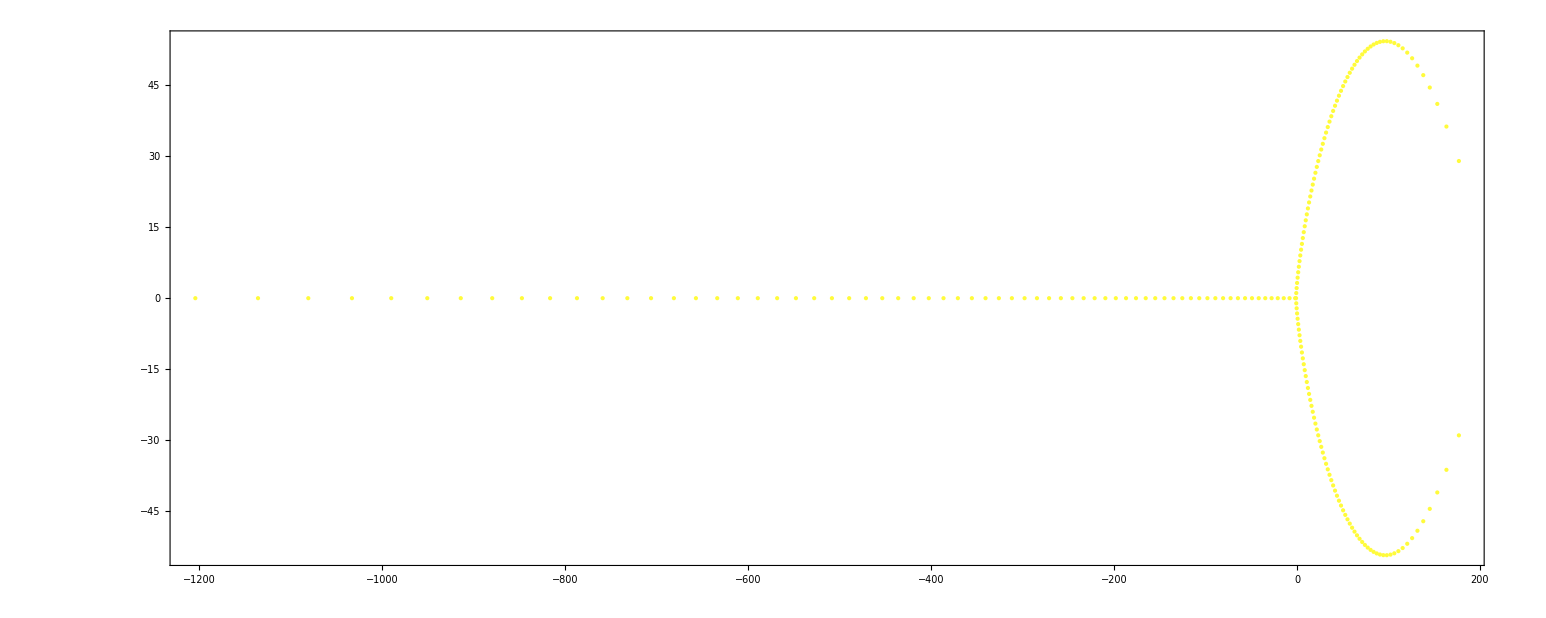

```mathematica
Graphics[Table[{colfunc[100],Point[{Re[#],Im[#]}]}&/@N@pocxrootsa[200,3,1],{n,1,1}],Frame->True]
```

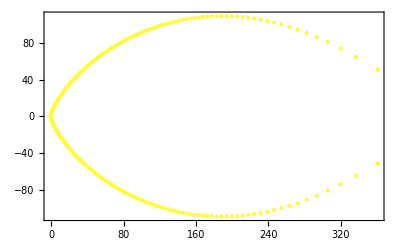

```mathematica
Graphics[Table[{colfunc[100],Point[{Re[#],Im[#]}]}&/@N@pocxrootsa[200,2,1],{n,1,1}],Frame->True]
```

```mathematica
N@Sum[ -1/r,{r,pocxrootsa[200,3,1]}]
```

1.1036+0. ⅈ

```mathematica
Chop@N@Product[1 -1/r,{r,pocxrootsa[200,3,1]}]
```

3.

```mathematica
N@Sum[ -1/r,{r,pocxrootsa[200,4,1]}]
```

1.37883+0. ⅈ

```mathematica
Chop@N@Product[1 -1/r,{r,pocxrootsa[200,4,1]}]
```

4.

```mathematica
Log[4.]
```

1.38629

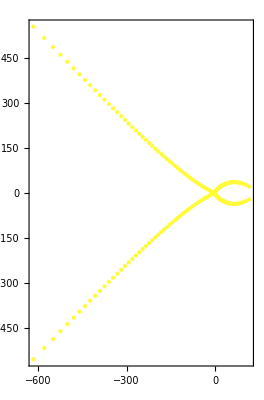

```mathematica
Graphics[Table[{colfunc[100],Point[{Re[#],Im[#]}]}&/@N@pocxrootsa[200,4,1],{n,1,1}],Frame->True]
```

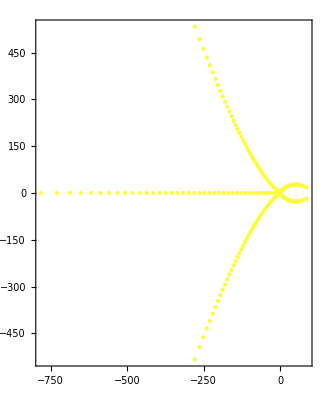

```mathematica
Graphics[Table[{colfunc[100],Point[{Re[#],Im[#]}]}&/@N@pocxrootsa[200,5,1],{n,1,1}],Frame->True]
```

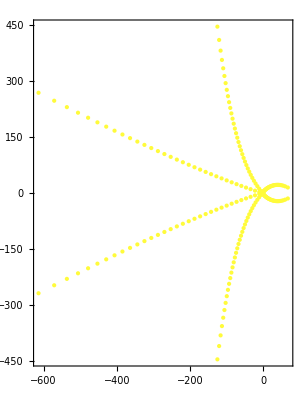

```mathematica
Graphics[Table[{colfunc[100],Point[{Re[#],Im[#]}]}&/@N@pocxrootsa[200,6,1],{n,1,1}],Frame->True]
```

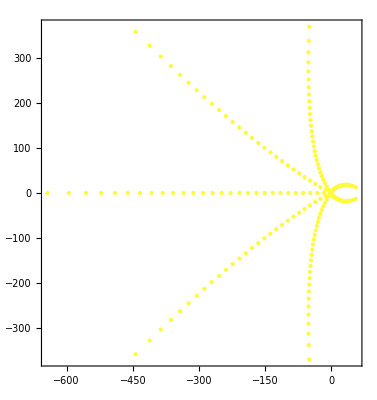

```mathematica
Graphics[Table[{colfunc[100],Point[{Re[#],Im[#]}]}&/@N@pocxrootsa[200,7,1],{n,1,1}],Frame->True]
```

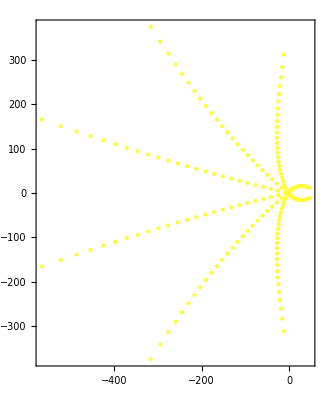

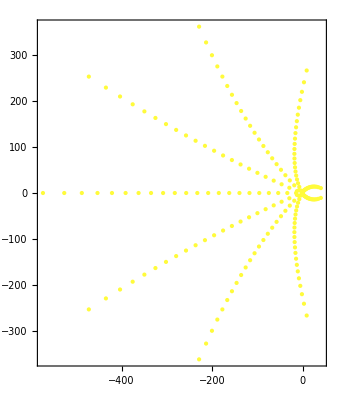

```mathematica
Graphics[Table[{colfunc[100],Point[{Re[#],Im[#]}]}&/@N@pocxrootsa[200,8,1],{n,1,1}],Frame->True]

Graphics[Table[{colfunc[100],Point[{Re[#],Im[#]}]}&/@N@pocxrootsa[200,9,1],{n,1,1}],Frame->True]
```

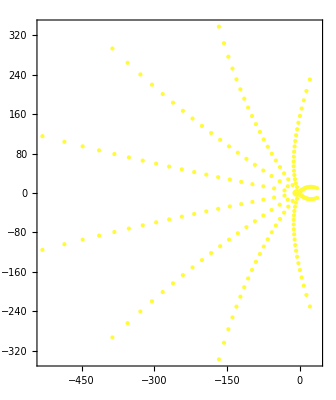

```mathematica
Graphics[Table[{colfunc[100],Point[{Re[#],Im[#]}]}&/@N@pocxrootsa[200,10,1],{n,1,1}],Frame->True]
```

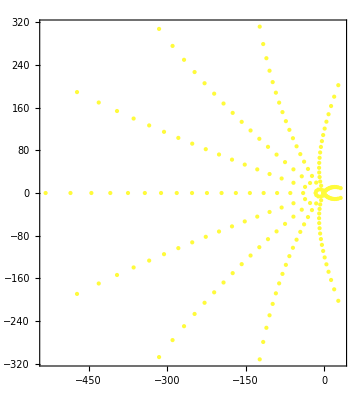

```mathematica
Graphics[Table[{colfunc[100],Point[{Re[#],Im[#]}]}&/@N@pocxrootsa[200,11,1],{n,1,1}],Frame->True]
```

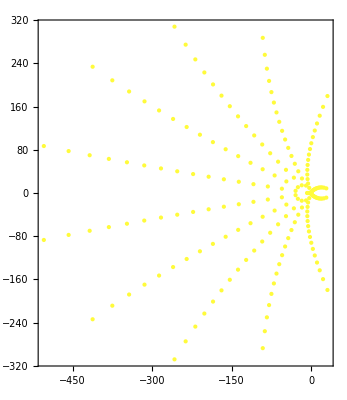

```mathematica
Graphics[Table[{colfunc[100],Point[{Re[#],Im[#]}]}&/@N@pocxrootsa[200,12,1],{n,1,1}],Frame->True]
```

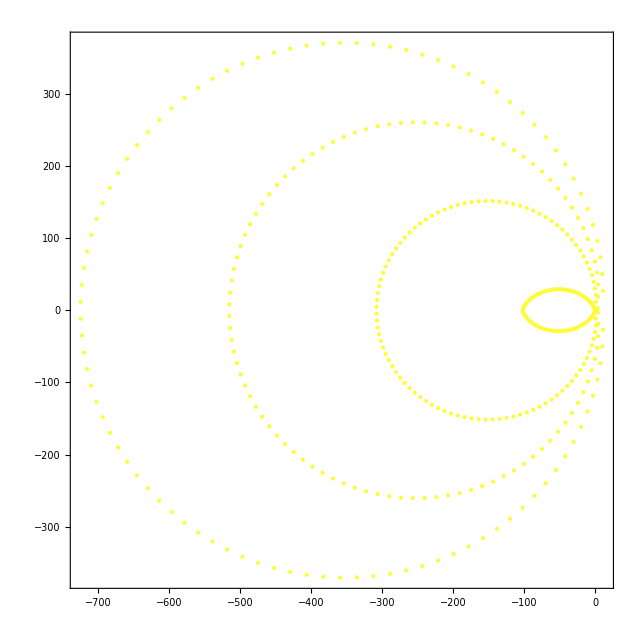

```mathematica
Graphics[Table[{colfunc[100],Point[{Re[#],Im[#]}]}&/@N@pocxrootsa[400,100,1],{n,1,1}],Frame->True]
```

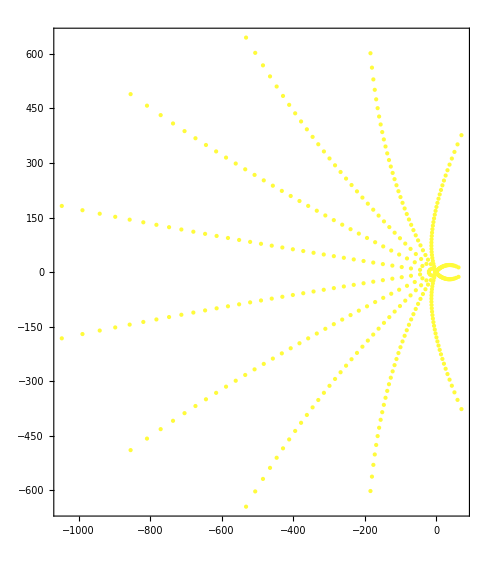

```mathematica
Graphics[Table[{colfunc[100],Point[{Re[#],Im[#]}]}&/@N@pocxrootsa[400,12,1],{n,1,1}],Frame->True]
```

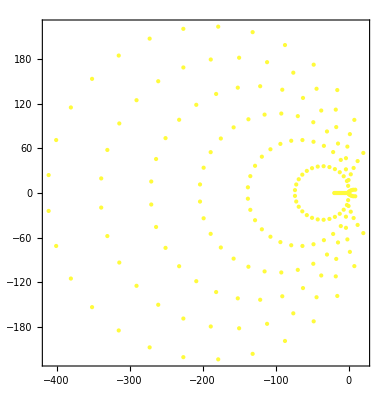

```mathematica
Graphics[Table[{colfunc[100],Point[{Re[#],Im[#]}]}&/@N@pocxrootsa[200,30,1],{n,1,1}],Frame->True]
```

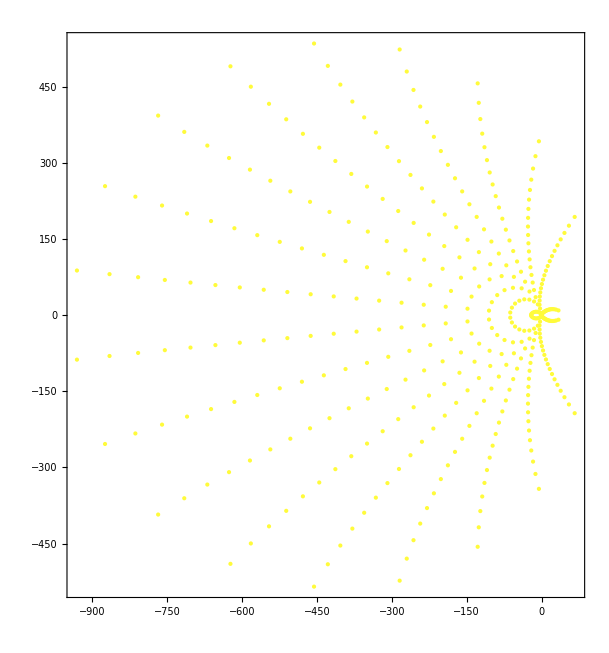

```mathematica
Graphics[Table[{colfunc[100],Point[{Re[#],Im[#]}]}&/@N@pocxrootsa[400,20,1],{n,1,1}],Frame->True]
```

```mathematica
poccrootsa[8]
```

{-8,-7,-6,-5,-4,-3,-2,-1}

```mathematica
Expand@pocc[8,z]
```

1+(761 z)/280+(29531 z^2)/10080+(267 z^3)/160+(1069 z^4)/1920+(9 z^5)/80+(13 z^6)/960+z^7/1120+z^8/40320

```mathematica
Expand@(Product[ (z+k),{k,1,8}]/8!)
```

1+(761 z)/280+(29531 z^2)/10080+(267 z^3)/160+(1069 z^4)/1920+(9 z^5)/80+(13 z^6)/960+z^7/1120+z^8/40320

```mathematica
Expand[Pochhammer[z+1,8]/8!]
```

1+(761 z)/280+(29531 z^2)/10080+(267 z^3)/160+(1069 z^4)/1920+(9 z^5)/80+(13 z^6)/960+z^7/1120+z^8/40320

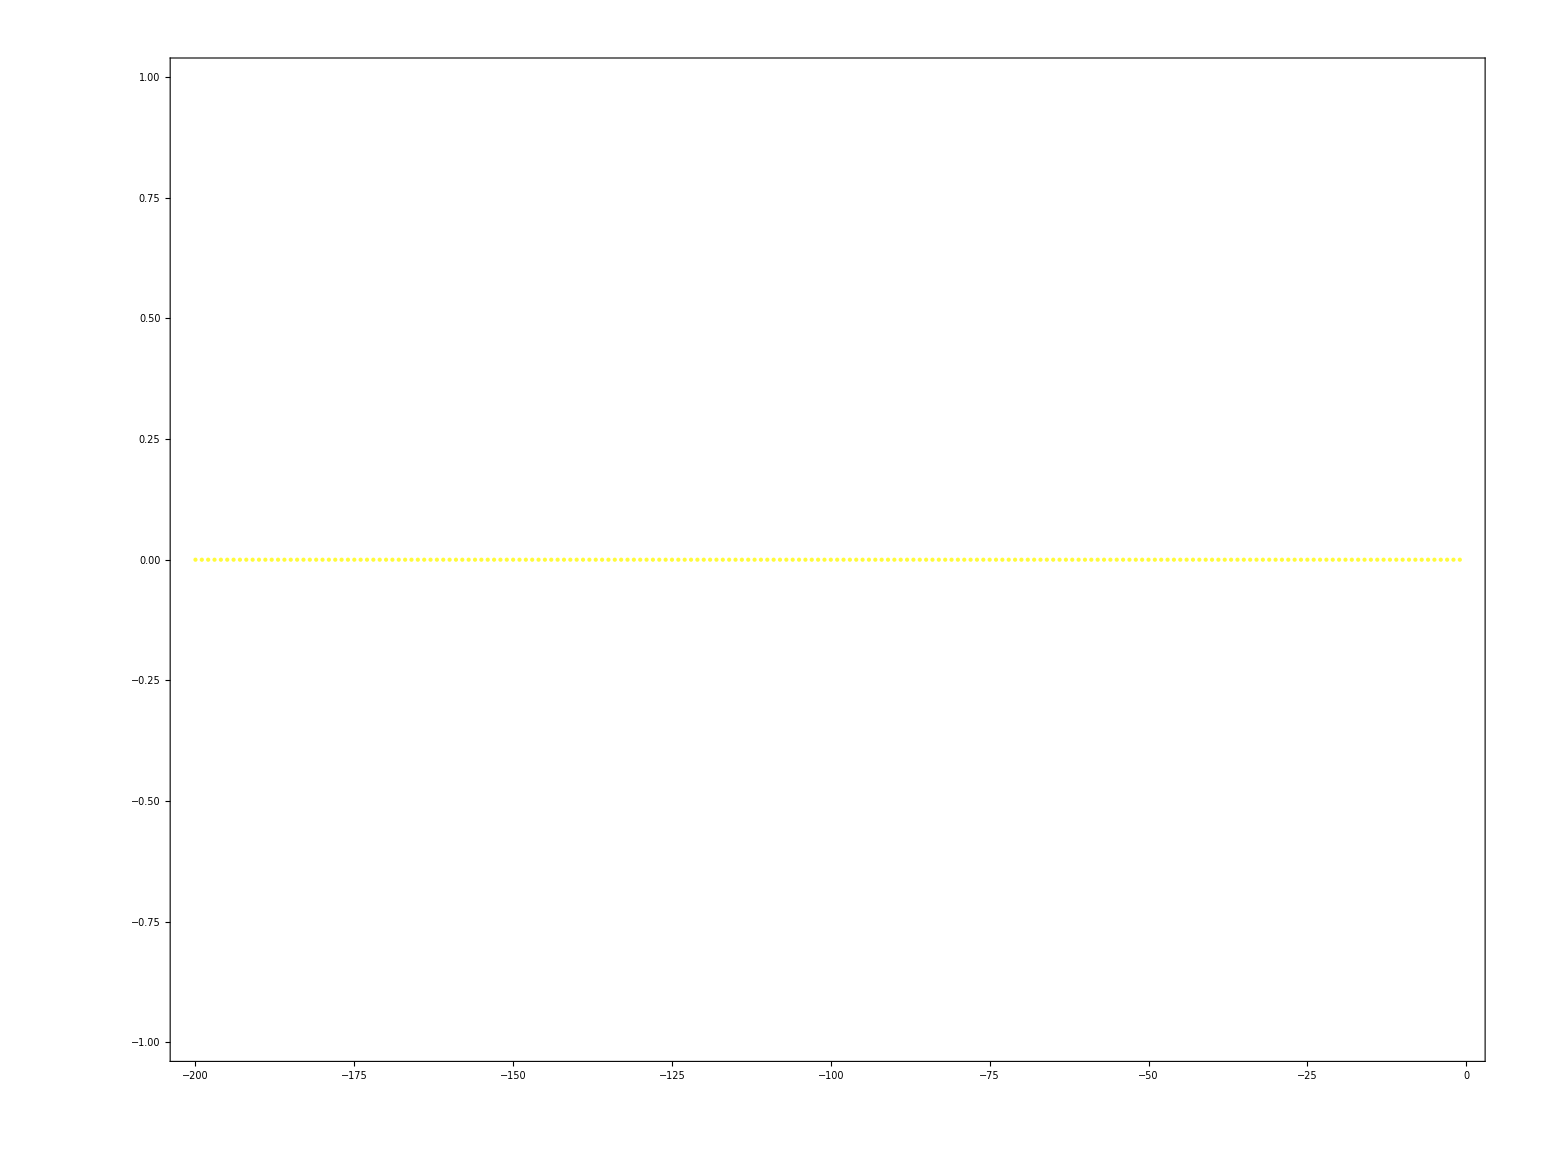

```mathematica
Graphics[Table[{colfunc[100],Point[{Re[#],Im[#]}]}&/@N@poccrootsa[200],{n,1,1}],Frame->True]
```

```mathematica
Graphics[Table[{colfunc[100],Point[{Re[#],Im[#]}]}&/@N@pocxrootsa[20,20,1],{n,1,1}],Frame->True]
```

```mathematica
pts4=Table[{Point[{Re[#],Im[#]}]}&/@pocxrootsa[n,12,1],{n,1,200}];
```

```mathematica
ListAnimate[Table[Graphics[pts4[[k]],Frame->True,Axes->True,AxesOrigin->{0,0}, PlotRange->{{-1000,100},{-500,500}}],{k,1,Length[pts4]}]]
```

```mathematica
pts4
```

```mathematica
pocx[50,1,2,-4]
```

16